```mathematica
l[a_,b_,c_,d_,e_,f_,g_,h_]:=h+Sum[x,{x,18-e-f-g,18-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,18-e-f,18-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,18-e,18}]-1350+4845*(d+Sum[x,{x,22-a-b-c,22-a-b}]+Sum[Sum[y,{y,0,x}]+1,{x,22-a-b,22-a}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,22-a,22}]-2324)
```

```mathematica
l[0,0,0,1,0,0,0,0]
```

4845

```mathematica
23!/16!/24
```

51482970

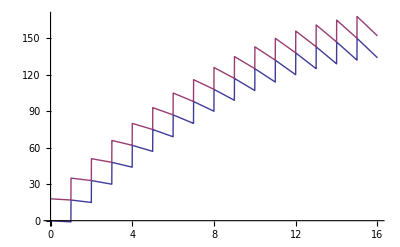

```mathematica
Plot[{l[0,0,0,0,0,0,x,0],Sum[y,{y,18-x,18}]},{x,0,16}]
```

```mathematica
h+Sum[x,{x,18-e-f-g,18-e-f}]+Sum[Sum[y,{y,0,x}]+1,{x,18-e-f,18-e}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,18-e,18}]-1350+4845*(d+Sum[x,{x,22-a-b-c,22-a-b}]+Sum[Sum[y,{y,0,x}]+1,{x,22-a-b,22-a}]+Sum[Sum[Sum[z,{z,0,y}]+1,{y,0,x}]+1,{x,22-a,22}]-2324)
```

4842+4845 (10623-1/24 (-21+a) (-12456+1598 a-69 a^2+a^3)+1/6 (1+b) (1524-135 a+3 a^2-67 b+3 a b+b^2)-1/2 (1+c) (-44+2 a+2 b+c)+d)-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032-111 e+3 e^2-55 f+3 e f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h

```mathematica
Expand[%]
```

(36700875 a)/4-(4901525 a^2)/8+(72675 a^3)/4-(1615 a^4)/8+(2343365 b)/2-106590 a b+(4845 a^2 b)/2-53295 b^2+(4845 a b^2)/2+(1615 b^3)/2+(208335 c)/2-4845 a c-4845 b c-(4845 c^2)/2+4845 d+(12617 e)/12-(2051 e^2)/24+(37 e^3)/12-e^4/24+(971 f)/6-18 e f+(e^2 f)/2-9 f^2+(e f^2)/2+f^3/6+(35 g)/2-e g-f g-g^2/2+h

```mathematica
Simplify[l[a,b,c,d,e,f,g,h],{a,b,c,d,e,f,g,h}∈Integers,ComplexityFunction->t]
```

4842+4845 (10623-1/24 (-21+a) (-12456+1598 a-69 a^2+a^3)+1/6 (1+b) (1524+3 a^2+3 a (-45+b)-67 b+b^2)-1/2 (1+c) (-44+2 a+2 b+c)+d)-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032+3 e^2+3 e (-37+f)-55 f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h

```mathematica
Simplify[l[a,b,c,d,e,f,g,h],{a,b,c,d,e,f,g,h}∈Integers]
```

4842-1615/8 (-90 a^3+a^4+a^2 (3035-12 b)-6 a (7575-88 b+2 b^2-4 c)-4 (-66 b^2+b^3+b (1451-6 c)+129 c-3 c^2+6 d))-1/24 (-17+e) (-7104+1094 e-57 e^2+e^3)+1/6 (1+f) (1032+3 e^2+3 e (-37+f)-55 f+f^2)-1/2 (1+g) (-36+2 e+2 f+g)+h

```mathematica
t[%]
```

30

```mathematica
CForm[%]
```

4842 - (1615*(-90*Power(a,3) + Power(a,4) + Power(a,2)*(3035 - 12*b) - 6*a*(7575 - 88*b + 2*Power(b,2) - 4*c) - 
        4*(-66*Power(b,2) + Power(b,3) + b*(1451 - 6*c) + 129*c - 3*Power(c,2) + 6*d)))/8. - 
   ((-17 + e)*(-7104 + 1094*e - 57*Power(e,2) + Power(e,3)))/24. + 
   ((1 + f)*(1032 + 3*Power(e,2) + 3*e*(-37 + f) - 55*f + Power(f,2)))/6. - ((1 + g)*(-36 + 2*e + 2*f + g))/2. + h

```mathematica
t[x_]:=Tr@((Length[#]-1)&/@(Extract[x,{Sequence@@Drop[#,-1]}]&/@Position[x,Times]))
```

```mathematica
t[a b c+d e]
```

3

```mathematica
Timing
```